# Illustration of nearest neighbour classification

Let’s look at some random data along a line with small modulation

```mathematica
Clear[data]
```

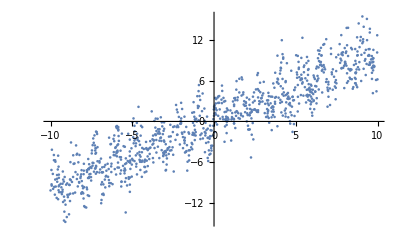

```mathematica
data=Table[x->x+2Sin[5x]+RandomVariate[NormalDistribution[0, 2]], {x, RandomReal[{-10, 10}, 1000]}];
ListPlot[List@@@data]
```

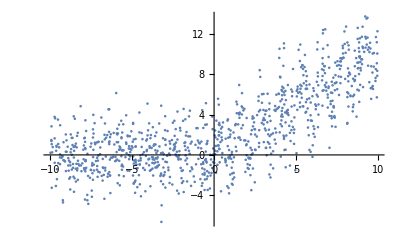

```mathematica
data=Table[x->Max[{0,x+2Sin[5x]}]+RandomVariate[NormalDistribution[0, 2]], {x, RandomReal[{-10, 10}, 1000]}];
ListPlot[List@@@data]
```

We will just fit the data using different numbers of nearest neighbours.

```mathematica
p=Predict[data,Method->{"NearestNeighbors","NeighborsNumber"->10}]
p2=Predict[data,Method->{"NearestNeighbors","NeighborsNumber"->500}]
```

PredictorFunction[…]

PredictorFunction[…]

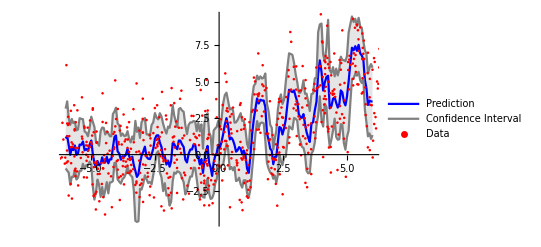

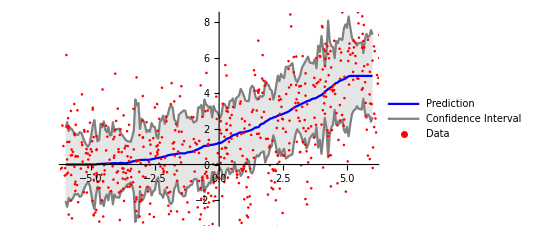

```mathematica
Show[Plot[{p[x],
p[x]+StandardDeviation[p[x,"Distribution"]],p[x]-StandardDeviation[p[x,"Distribution"]]},
{x,-6,6},
PlotStyle->{Blue,Gray,Gray},
Filling->{2->{3}},
Exclusions->False,PerformanceGoal->"Speed",PlotLegends->{"Prediction","Confidence Interval"}],ListPlot[List@@@data,PlotStyle->Red,PlotLegends->{"Data"}]]
Show[Plot[{p2[x],
p2[x]+StandardDeviation[p[x,"Distribution"]],p2[x]-StandardDeviation[p[x,"Distribution"]]},
{x,-6,6},
PlotStyle->{Blue,Gray,Gray},
Filling->{2->{3}},
Exclusions->False,PerformanceGoal->"Speed",PlotLegends->{"Prediction","Confidence Interval"}],ListPlot[List@@@data,PlotStyle->Red,PlotLegends->{"Data"}]]
```